```mathematica
(*Defining the atmospheric density distribution*)
(*Height of point*)
h[p_] := Norm[p] - earthRadius;
(*Density of point. Very simple approximation linear*)
d[p_] := 1.0 - (h[p] / (stratoHeight - earthRadius));
(*Density along ray*)
d[t_, {dx_, dy_, dz_}, {ox_, oy_, oz_}] :=d[t*{dx,dy,dz}+ {ox,oy,oz}]

dt[t_] := FullSimplify[d[t, {dx, dy, dz}, {ox, oy, oz}],Assumptions->Element[{t,dx,dy,dz,ox,oy,oz},Reals]]
(*Integral*)
idt := ∫(dt[t])ⅆt
```

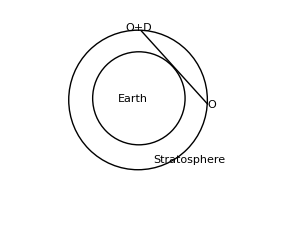

```mathematica
dt[t]
idt
```

(-1. stratoHeight+√((ox+dx t)^2+(oy+dy t)^2+(oz+dz t)^2))/(earthRadius-1. stratoHeight)

1/(earthRadius-1. stratoHeight)(-1. stratoHeight t+((dx ox+dy oy+dz oz)/(2 (dx^2+dy^2+dz^2))+t/2) √(ox^2+oy^2+oz^2+2 dx ox t+2 dy oy t+2 dz oz t+dx^2 t^2+dy^2 t^2+dz^2 t^2)+1/(2 (dx^2+dy^2+dz^2)^(3/2))(dy^2 ox^2+dz^2 ox^2-2 dx dy ox oy+dx^2 oy^2+dz^2 oy^2-2 dx dz ox oz-2 dy dz oy oz+dx^2 oz^2+dy^2 oz^2) Log[dx ox+dy oy+dz oz+dx^2 t+dy^2 t+dz^2 t+√(dx^2+dy^2+dz^2) √(ox^2+oy^2+oz^2+2 dx ox t+2 dy oy t+2 dz oz t+dx^2 t^2+dy^2 t^2+dz^2 t^2)])

```mathematica
(*Integral of the density along the ray t=0 to t=1*)
```

```mathematica
s = (idt /. t->1) - (idt /. t ->0);
fss = FullSimplify[s]
```

1/(2 (earthRadius-1. stratoHeight))(-((dx ox+dy oy+dz oz) √(ox^2+oy^2+oz^2))/(dx^2+dy^2+dz^2)+((dx (dx+ox)+dy (dy+oy)+dz (dz+oz)) √((dx+ox)^2+(dy+oy)^2+(dz+oz)^2))/(dx^2+dy^2+dz^2)-2. stratoHeight-1/(dx^2+dy^2+dz^2)^(3/2)(dz^2 (ox^2+oy^2)-2 dx dz ox oz-2 dy oy (dx ox+dz oz)+dy^2 (ox^2+oz^2)+dx^2 (oy^2+oz^2)) Log[dx ox+dy oy+dz oz+√(dx^2+dy^2+dz^2) √(ox^2+oy^2+oz^2)]+1/(dx^2+dy^2+dz^2)^(3/2)(dz^2 (ox^2+oy^2)-2 dx dz ox oz-2 dy oy (dx ox+dz oz)+dy^2 (ox^2+oz^2)+dx^2 (oy^2+oz^2)) Log[dx (dx+ox)+dy (dy+oy)+dz (dz+oz)+√(dx^2+dy^2+dz^2) √((dx+ox)^2+(dy+oy)^2+(dz+oz)^2)])

```mathematica
(*Translating formula to C code (used on GLSL). All powers of two had to be translated to multiplications as GLSL pow() is undefined for negative values on some platforms.*)
fsss = fss /.
 dx^2+dy^2+dz^2 -> ld /.
dx ox+dy oy+dz oz->pdo /.
 (dx+ox)^2->dox2 /.
(dy+oy)^2->doy2 /.
 (dz+oz)^2-> doz2 /.
ox^2->ox2 /.
oy^2->oy2 /.
oz^2->oz2/.
dx^2->dx2/.
dy^2->dy2/.
dz^2->dz2
```

1/(2 (earthRadius-1. stratoHeight))((√(dox2+doy2+doz2) (dx (dx+ox)+dy (dy+oy)+dz (dz+oz)))/ld-(√(ox2+oy2+oz2) pdo)/ld-2. stratoHeight+1/ld^(3/2)(dz2 (ox2+oy2)-2 dx dz ox oz-2 dy oy (dx ox+dz oz)+dy2 (ox2+oz2)+dx2 (oy2+oz2)) Log[√(dox2+doy2+doz2) √ld+dx (dx+ox)+dy (dy+oy)+dz (dz+oz)]-1/ld^(3/2)(dz2 (ox2+oy2)-2 dx dz ox oz-2 dy oy (dx ox+dz oz)+dy2 (ox2+oz2)+dx2 (oy2+oz2)) Log[√ld √(ox2+oy2+oz2)+pdo])

```mathematica
code = CForm[fsss]
```

((Sqrt(dox2 + doy2 + doz2)*(dx*(dx + ox) + dy*(dy + oy) + dz*(dz + oz)))/ld - 
     (Sqrt(ox2 + oy2 + oz2)*pdo)/ld - 2.*stratoHeight + 
     ((dz2*(ox2 + oy2) - 2*dx*dz*ox*oz - 2*dy*oy*(dx*ox + dz*oz) + dy2*(ox2 + oz2) + dx2*(oy2 + oz2))*
        Log(Sqrt(dox2 + doy2 + doz2)*Sqrt(ld) + dx*(dx + ox) + dy*(dy + oy) + dz*(dz + oz)))/Power(ld,1.5)
       - ((dz2*(ox2 + oy2) - 2*dx*dz*ox*oz - 2*dy*oy*(dx*ox + dz*oz) + dy2*(ox2 + oz2) + dx2*(oy2 + oz2))*
        Log(Sqrt(ld)*Sqrt(ox2 + oy2 + oz2) + pdo))/Power(ld,1.5))/(2.*(earthRadius - 1.*stratoHeight))